# Edge length vs T

## load data

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039, 0.03105 ,0.025, 0.016, 0.01 ,0.008, 0.0063 ,0.005, 0.00385 ,0.0031 , 0.0028 ,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015,0.001, 0.00067 ,0.0005},{0.039, 0.016 ,0.01 ,0.005, 0.00385 ,0.0025, 0.002, 0.001, 0.0005, 0.00033, 0.00025 ,0.00014 ,0.000091, 0.000077,0.000054, 0.000045 ,0.000036}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 3, 4,8, 15, 40,70,150, 250, 600,2000 ,2500,4500,9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{2 ,4,10, 20, 40,60, 80,200, 500 ,800 ,1400, 2500 ,4200 ,5000, 6000,8500, 9500}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

## Edge length

### test with one snapshot

```mathematica
testData=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.00500000_waitingTime10000_idx16.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[<111,8192>, Real64],/postion→NumericArray[<111,8192>, Real64],/time→NumericArray[…],/type→NumericArray[<111,4096>, Integer32],/velocity→NumericArray[<111,8192>, Real64]|>

```mathematica
Head[testData]
```

Symbol

```mathematica
testData=!=$Failed
```

True

```mathematica
testPos=Partition[Normal[testData[[3,111]]],2];
```

```mathematica
testPos
```

```mathematica
edgeList[allPoints_,box_List]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD,edgeLists},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=allPointsPBD=Select[Flatten[translatedCopies[[1]],1],-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
AnnotationValue[{vm,1},MeshCellMeasure]
];
```

```mathematica
testPre=edgeList[testPos,{64,64}];
```

```mathematica
testPre=edgeList[testPos,{64,64}][[8]]
```

0.997002

```mathematica
testEdges=DeleteAdjacentDuplicates[Sort[testPre],Abs[#1-#2]<=0.0000001&];
```

```mathematica
testEdges[[;;10]]
```

{0.00706621,0.009983,0.0108383,0.0129789,0.0146639,0.0160973,0.0191805,0.0193781,0.0202882,0.0222535}

```mathematica
testEdges[[;;10]]
```

{0.000097455,0.000191741,0.00406228,0.0042484,0.00425976,0.00429476,0.0044811,0.00449633,0.00491993,0.00492705}

```mathematica
testEdges[[;;10]]
```

{0.0000105864,0.0000777787,0.00079024,0.000837429,0.00104079,0.00114447,0.00141648,0.00223896,0.00235705,0.00239761}

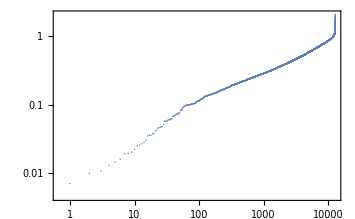

```mathematica
ListLogLogPlot[testEdges]
```

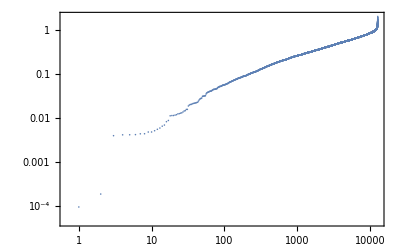

```mathematica
ListLogLogPlot[testEdges]
```

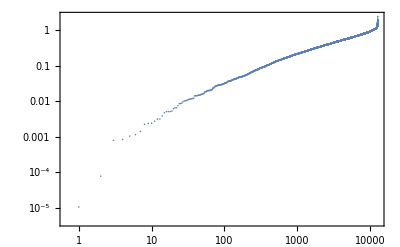

```mathematica
ListLogLogPlot[testEdges]
```

```mathematica
DeleteDuplicates[{0.01083829891055921,0.010838298910575821},Abs[#1-#2]<=0.0000001&]
```

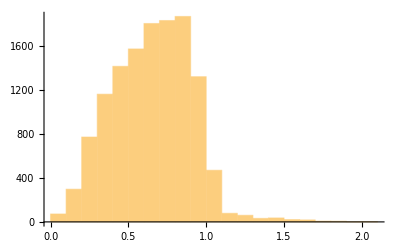

```mathematica
Histogram[testEdges]
```

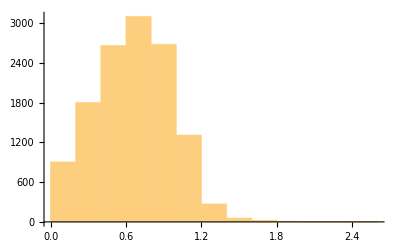

```mathematica
Histogram[testEdges]
```

```mathematica
0.01083829891055921
```

```mathematica
0.010838298910575821
```

```mathematica
binWidth=10;
testDis=Table[{(testEdges[[(i+1)*binWidth]]+testEdges[[i*binWidth]])/2,binWidth/(testEdges[[(i+1)*binWidth]]-testEdges[[i*binWidth]])/Length[testEdges]},{i,Floor[Length[testEdges]/binWidth]-2}];
```

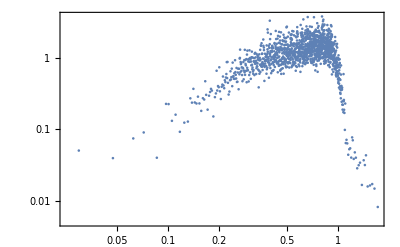

```mathematica
ListLogLogPlot[testDis]
```

### multiple Snapshots for p0, T

```mathematica
sortedEdgeList[filename_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD,edgeLists,box,allPoints,data},
data=Import[filename,"Data"];
If[data=!=$Failed,
allPoints={Partition[Normal[data[[3,1]]],2],Partition[Normal[data[[3,Ceiling[Length[data[[3]]]*9/10]]]],2],Partition[Normal[data[[3,Ceiling[Length[data[[3]]]*4/5]]]],2],Partition[Normal[data[[3,Ceiling[Length[data[[3]]]*3/5]]]],2],Partition[Normal[data[[3,Length[data[[3]]]]]],2]};
box={data[[1,1,1]],data[[1,1,4]]};
Sort[Flatten[Table[copies=Table[allPoints[[i]],9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Select[Flatten[translatedCopies[[1]],1],-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
edgeLists=AnnotationValue[{vm,1},MeshCellMeasure];
DeleteAdjacentDuplicates[Sort[edgeLists],Abs[#1-#2]<=0.0000001&],{i,Length[allPoints]}]]],{}
]
];
```

#### test

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.06300000_waitingTime10000_idx10.nc"]
```

{/BoxMatrix,/additionalData,/postion,/time,/type,/velocity}

```mathematica
sortedEdgeList["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.06300000_waitingTime10000_idx199.nc"]
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.06300000_waitingTime10000_idx199.nc not found during Import.

{}

```mathematica
Flatten[{{1,2},{}}]
```

{1,2}

```mathematica
Quantile[sortedEdgeList["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.06300000_waitingTime10000_idx10.nc"],1/100]
```

0.0314396

```mathematica
Quantile[sortedEdgeList["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.00500000_waitingTime10000_idx17.nc"],1/100]
```

0.070438

```mathematica
Quantile[sortedEdgeList["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.00250000_waitingTime10000_idx13.nc"],1/100]
```

0.0844072

```mathematica
Quantile[sortedEdgeList["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.00310000_waitingTime10000_idx16.nc"],1/100]
```

0.0840454

```mathematica
Quantile[sortedEdgeList["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T0.00067000_waitingTime50000_idx10.nc"],1/100]
```

0.121418

```mathematica
NonlinearModelFit[{{0.063,0.03143955302299278},{0.00500000,0.07043802451645834},{0.00250000,0.08440724908255949},{0.00310000,0.08404542872317353},{0.00067000,0.12141763569051334}},{A*x^B,{B<0.999}},{A,B},x]
```

FittedModel[…]

```mathematica
dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T","_waitingTime","_idx10.nc"},{temperatures[[2,T]],Floor[If[tauEstimate[[2,T]]==999999,tauEstimate[[2,T]],If[tauEstimate[[2,T]]<1000,10000,tauEstimate[[2,T]]*10]]]},{8,0}]
```

```mathematica
testLength=Table[sortedEdgeList[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T","_waitingTime","_idx10.nc"},{temperatures[[2,T]],Floor[If[tauEstimate[[2,T]]==999999,tauEstimate[[2,T]],If[tauEstimate[[2,T]]<1000,10000,tauEstimate[[2,T]]*10]]]},{8,0}]],{T,Length[temperatures[[2]]]}];
```

```mathematica
hunQuan=Table[Quantile[testLength[[T]],1/1000],{T,Length[temperatures[[2]]]}]
```

{0.00291853,0.00452796,0.00399957,0.00556467,0.00912163,0.00720135,0.00807073,0.00647678,0.00966617,0.0108191,0.0123364,0.0145194,0.0170457,0.0157922,0.0294148,0.0289236}

```mathematica
twoHun=Table[Mean[testLength[[T]][[;;100]]],{T,Length[temperatures[[2]]]}]
```

{0.00416443,0.00541903,0.00484867,0.00675535,0.0102778,0.00981632,0.010086,0.00892278,0.0116175,0.0141666,0.0153295,0.0177163,0.0205,0.0203935,0.0314865,0.0341861}

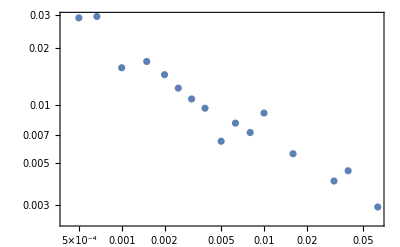

```mathematica
ListLogLogPlot[Table[{temperatures[[2,T]],hunQuan[[T]]},{T,Length[temperatures[[2]]]}]]
```

```mathematica
NonlinearModelFit[Table[{temperatures[[2,T]],hunQuan[[T]]},{T,Length[temperatures[[2]]]}],{A*x^B,{B<0.999}},{A,B},x]
```

FittedModel[…]

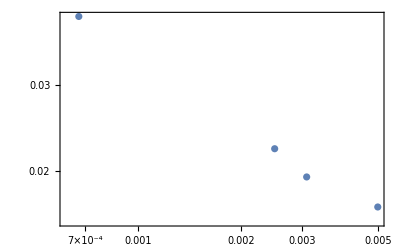

```mathematica
ListLogLogPlot[{{0.00500000,0.016907755574611803},{0.00250000,0.022245469118458726},{0.00310000,0.019475810013627467},{0.00067000,0.04146830241190219}}]
```

```mathematica
Boole[testData[[1]]==$Failed]
```

Boole[NumericArray[…]==$Failed]

```mathematica
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/glassyDynamics_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Table[For[],{p,Length[p0s]}]
```

#### all configurations

```mathematica
dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/glassyDynamics_N4096_p3.8250_T","_waitingTime","_idx10.nc"},{temperatures[[2,T]],Floor[If[tauEstimate[[2,T]]==999999,tauEstimate[[2,T]],If[tauEstimate[[2,T]]<1000,10000,tauEstimate[[2,T]]*10]]]},{8,0}]
```

```mathematica
dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/glassyDynamics_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}]
```

```mathematica
testLength=Table[Table[Flatten[Table[sortedEdgeList[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/glassyDynamics_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}]],{i,Length[records[[p]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/glassyDynamics_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/glassyDynamics_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.800/glassyDynamics_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
Dimensions[testLength[[1,1]]]
```

{449209}

```mathematica
Table[Table[Quantile[testLength[[p,T]],1/10000],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.000272759,0.000472113,0.00044454,0.000438171,0.000656683,0.000972181,0.00116188,0.00135781,0.00177691,0.00169128,0.00231994,0.00252059,0.00434448,0.00351251},{0.000281522,0.000380731,0.000318411,0.000580371,0.000630271,0.00081939,0.000827064,0.000763141,0.00100903,0.00117471,0.00127602,0.00103342,0.00146289,0.002312,0.00281593,0.00279504},{0.000361494,0.000406055,0.000466354,0.000529863,0.000767867,0.000800581,0.00095237,0.00120482,0.00128916,0.00109297,0.00134949,0.00162104,0.0013531,0.00179295,0.00176101,0.00181294,0.00157737}}

```mathematica
Table[Table[Quantile[testLength[[p,T]],1/100],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0321263,0.0390839,0.0430315,0.0475825,0.0587234,0.0742395,0.081632,0.0929068,0.102206,0.116142,0.130417,0.135392,0.142607,0.146711},{0.0283821,0.0335165,0.0360026,0.0473526,0.0565791,0.0601698,0.0654362,0.0698963,0.0755646,0.0815417,0.0841761,0.0907061,0.0977625,0.105121,0.116368,0.125654},{0.0300209,0.0388885,0.0423104,0.0499517,0.0528066,0.0569624,0.059678,0.0657358,0.0704207,0.0733707,0.0760348,0.0789726,0.0799209,0.0836945,0.0823842,0.0837433,0.0846328}}

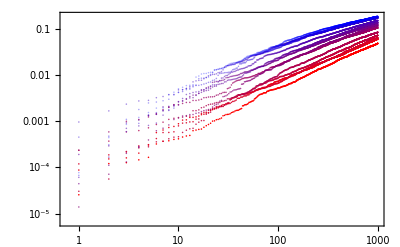
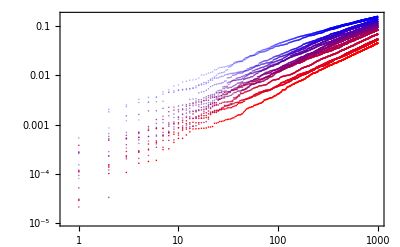
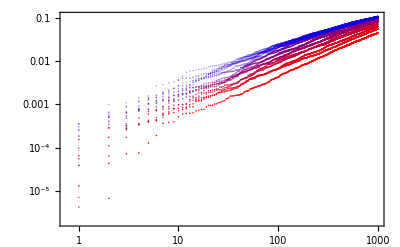

```mathematica
Table[ListLogLogPlot[Table[testLength[[p,T,;;1000]],{T,Length[temperatures[[p]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]]],{p,Length[p0s]}]
```

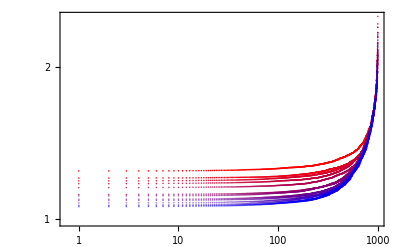
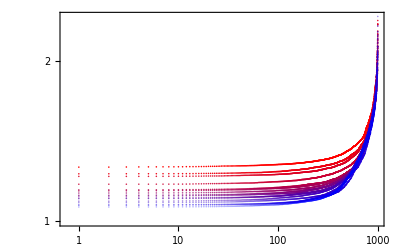
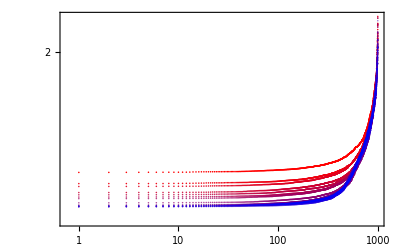

```mathematica
Table[ListLogLogPlot[Table[testLength[[p,T,Length[testLength[[p,T]]]-1000;;]],{T,Length[temperatures[[p]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]]],{p,Length[p0s]}]
```